```mathematica
Clear["Global`*"]
```

## Compressive Tidal Fields

### Constants Definition

```mathematica
parsec := 3.086  10^16 (*m*)
G := 6.674 10^-11 /parsec^3 (*parsec^3 kg^-1 s^-2*)
Msun:= 1.988435 10^30(*kg*)
ΣMilkyway := 640.9 * Msun   (* Kg parsec^-2*)
ρMilkyway := 0.035* Msun (* Kg pc^-3*)
RcMilkyway := 5*10^3 (*halo radius pc*)
RdMilkyway := 3.2 10^3(*disk radius pc*)
```

```mathematica
M := 1
r0 := 1
v0 := 1
ρ0 :=1
Σ0 := 1
```

```mathematica
ρUGC7321 := 0.057* Msun (* Kg pc^-3*)
RcUGC7321 := 2500 (*halo radius pc*)
ΣUGC7231 := 50.2 * Msun(* Kg parsec^-2*)
RdUGC7321:= 2100 (*disk radius parsec*)
```

### Potential and Tides definition

```mathematica
Tplummer[r_]:= - G M (1 -2 (r/r0)^2)/(r0^3(1 + (r/r0)^2)^(5/2))
```

```mathematica
Tlog[r_] := G  v0^2(r^2-1)/(r0^2(r^2+1)^2)
```

```mathematica
Thernquist[r_] := 2G M/(r0^3(1+r)^3)
```

```mathematica
Tnfw[r_]:= 4Pi G ρ0 (r0/r)^3(2 Log[1+ r/r0] - (3 r^2+2 r r0)/(r+r0)^2)
```

```mathematica
Vexponential[r_]:= -Pi G Σ0 r(BesselI[r/r0,0] BesselK[r/r0,1] - BesselI[r/r0,1] BesselK[r/r0,0] )
```

```mathematica
Texponential[x_]:=2Pi G (Σ/rd) ( 2 x/rd(BesselI[0,x/rd]BesselK[1,x/rd]-BesselI[1,x/rd]BesselK[0,x/rd])-BesselI[0,x/rd]BesselK[0,x/rd]-BesselI[1,x/rd]BesselK[1,x/rd])
```

```mathematica
Subscript[ϕ, halo][x_,y_,z_] := -(4*Pi*G*ρ*rc^2)(0.5*Log[r0^2+x^2+y^2+z^2]+r0/(√(x^2+y^2+z^2))*ArcTan[(√(x^2+y^2+z^2))/r0 ]-1)
```

```mathematica
Thalo[x_,y_,z_]:=-4 π G*ρ*rc^2*(-(2. x^2)/((1+x^2+y^2+z^2)^2)-(2 x^2)/((x^2+y^2+z^2) (1+x^2+y^2+z^2)^2)+1./(1+x^2+y^2+z^2)-(3 x^2)/((x^2+y^2+z^2)^2 (1+x^2+y^2+z^2))+1/((x^2+y^2+z^2) (1+x^2+y^2+z^2))+(3 x^2 ArcTan[√(x^2+y^2+z^2)])/((x^2+y^2+z^2)^(5/2))-ArcTan[√(x^2+y^2+z^2)]/((x^2+y^2+z^2)^(3/2)))
```

```mathematica
Thalo[x,0,0]
```

-2.8537×10^-59 rc^2 ρ (-2/((1+x^2)^2)-(2. x^2)/((1+x^2)^2)+1./(1+x^2)-2/(x^2 (1+x^2))+(2 ArcTan[√(x^2)])/((x^2)^(3/2)))

```mathematica
Texponential[x]
```

(1.42685×10^-59 Σ (-BesselI[0,x/rd] BesselK[0,x/rd]-BesselI[1,x/rd] BesselK[1,x/rd]+(2 x (-BesselI[1,x/rd] BesselK[0,x/rd]+BesselI[0,x/rd] BesselK[1,x/rd]))/rd))/rd

```mathematica
Thaloplusexp[x_,y_,z_] := Thalo[x,y,z]+Texponential[x]
```

### Milky way

Check for the halo tidal field it is supposed to peak near 5kpc

```mathematica
ρ[R_] := ρMilkyway/(1+R^2/RcMilkyway^2)
```

```mathematica
Subscript[ϕ, halo][x_,y_,z_] := -(4*Pi*G*ρMilkyway*RcMilkyway^2)(0.5*Log[RcMilkyway^2+x^2+y^2+z^2]+RcMilkyway/(√(x^2+y^2+z^2))*ArcTan[(√(x^2+y^2+z^2))/RcMilkyway ]-1)
```

```mathematica
Texponential[x_]:=2Pi G (Σ/rd) ( 2 x/rd(BesselI[0,x/rd]BesselK[1,x/rd]-BesselI[1,x/rd]BesselK[0,x/rd])-BesselI[0,x/rd]BesselK[0,x/rd]-BesselI[1,x/rd]BesselK[1,x/rd])
```

```mathematica
Thalo2511[x_]:= -(4 Pi G ρMilkyway RcMilkyway^2) ((RcMilkyway^2-x^2)/((RcMilkyway^2+x^2)^2)- (1+ 3 x^2/RcMilkyway^2)/(x^2(1+ x^2/RcMilkyway^2)^2) - RcMilkyway/x^3  (x/(RcMilkyway (1+ x^2/RcMilkyway^2))- 2ArcTan[x/RcMilkyway]))
```

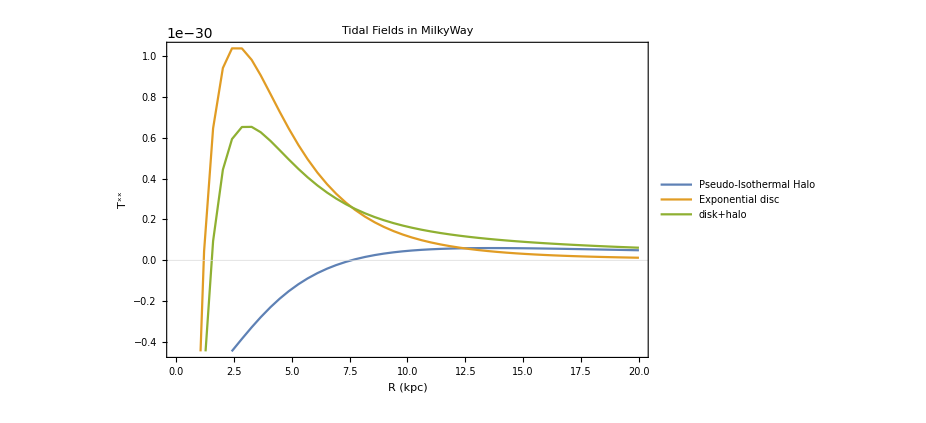

```mathematica
Plot[{Thalo2511[x*1000],Texponential[x*1000]/.{Σ -> ΣMilkyway,rd-> RdMilkyway},(Thalo2511[x*1000]+Texponential[x*1000]/.{Σ -> ΣMilkyway,rd-> RdMilkyway})},{x,0,20},PlotLegends->Placed[{"Pseudo-Isothermal Halo","Exponential disc","disk+halo"},{.8,.7}],FrameLabel->{HoldForm[R "(kpc)"],HoldForm[T^xx]},LabelStyle->{GrayLevel[0]},Frame->True,PlotLabel->HoldForm["Tidal Fields in MilkyWay"],LabelStyle->Directive[Bold, Medium],GridLines->{{0,3.2,5,7.574973,1.5297},{0}},GridLinesStyle->{{Orange, Dashed}, {Purple, Dotted}},PlotRange->Automatic]
```

```mathematica
T0MW[x_] := (Thalo2511[x*1000]+Texponential[x*1000]/.{Σ -> ΣMilkyway,rd-> RdMilkyway})parsec^2
```

```mathematica
T0MW[1]
```

-1092.01

```mathematica
T0MW[0.5]
```

-3792.51

```mathematica
T0MW[2]
```

407.966

Units of T^xx is potential/x^2 = force/M x = M L T^-2/ML = T^-2  = (km/kpc)^2  T^-2  = ((1000/1000*parsec)^2) sec^-2

```mathematica
rhoEffMW[x_] := T0MW[x]/(4 Pi G)
```

```mathematica
Vhalo[r_] :=2 √π √(G r RcMilkyway^2 ρMilkyway (1/(r (1+r^2/RcMilkyway^2))+(1. r)/(r^2+RcMilkyway^2)-(r RcMilkyway ArcTan[(√(r^2))/RcMilkyway])/((r^2)^(3/2))))
```

```mathematica
Vd[R_] :=   √((Pi*G*ΣMilkyway/RdMilkyway)(R^2 BesselI[0,R/(2*RdMilkyway)] BesselK[0,R/(2*RdMilkyway)]-R^2 BesselI[1,R/(2*RdMilkyway)] BesselK[1,R/(2*RdMilkyway)]))
```

```mathematica
Vnet[R_] := √(Vhalo[R]^2 + Vd[R]^2)
```

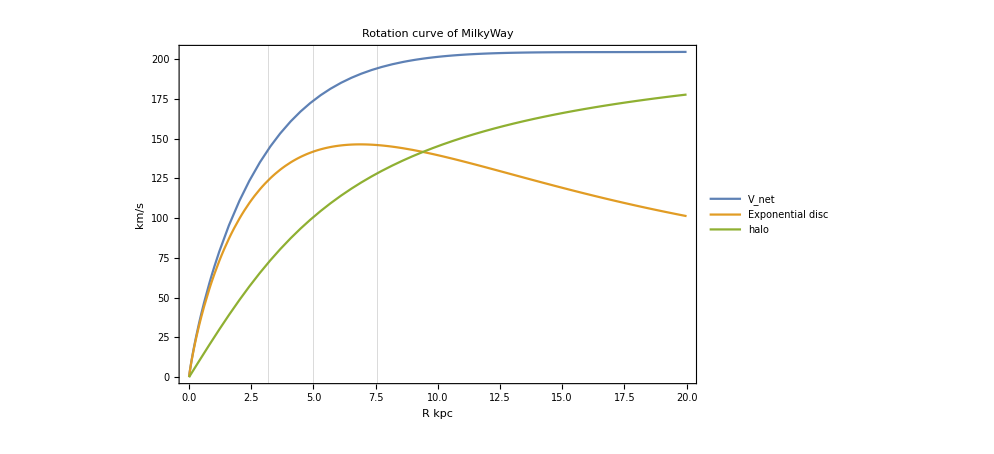

```mathematica
Plot[{Vnet[R*1000](3.086  10^13),Vd[R*1000](3.086  10^13),Vhalo[R*1000](3.086  10^13)},{R,0,20},FrameLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of MilkyWay],LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{"V_net","Exponential disc","halo"},{.8,.3}],GridLines->{{3.2,5,7.574973},{}},Frame->True]
```

### UGC 7321

```mathematica
Thalougc[x_]:= -(4 Pi G ρUGC7321 RcUGC7321^2) ((RcUGC7321^2-x^2)/((RcUGC7321^2+x^2)^2)- (1+ 3 x^2/RcUGC7321^2)/(x^2(1+ x^2/RcUGC7321^2)^2) - RcUGC7321/x^3  (x/(RcUGC7321 (1+ x^2/RcUGC7321^2))- 2ArcTan[x/RcUGC7321]))
```

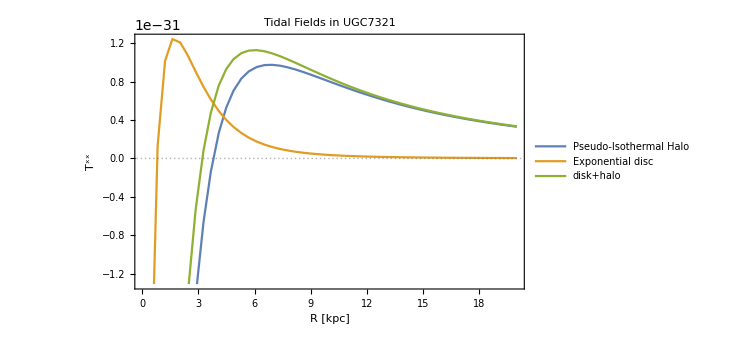

```mathematica
Plot[{Thalougc[x*1000],Texponential[x*1000]/.{Σ -> ΣUGC7231,rd-> RdUGC7321},(Thalougc[x*1000]+Texponential[x*1000]/.{Σ -> ΣUGC7231,rd-> RdUGC7321})},{x,0,20},PlotLegends->Placed[{"Pseudo-Isothermal Halo","Exponential disc","disk+halo"},{.8,.3}],FrameLabel->{HoldForm[R "[kpc]"],HoldForm[T^xx]},LabelStyle->{GrayLevel[0]},Frame->True,PlotTheme->"Detailed",PlotLabel->HoldForm["Tidal Fields in UGC7321"],LabelStyle->Directive[Bold, Medium],GridLines->{{0.79,3.2,3.79},{0}},PlotRange->Automatic]
```

```mathematica
T0UGC7321[x_] := (Thalougc[x*1000]+Texponential[x*1000]/.{Σ -> ΣUGC7231,rd-> RdUGC7321}) parsec^2
```

```mathematica
T0UGC7321[2]
```

-255.457

```mathematica
T0UGC7321[1]
```

-715.938

```mathematica
T0UGC7321[0.5]
```

-1127.45

```mathematica
T0UGC7321[2]
```

-255.457

```mathematica
T0UGC7321[5]
```

100.741

```mathematica
Vhalougc[r_] :=2 √π √(G r RcUGC7321^2 ρUGC7321(1/(r (1+r^2/RcUGC7321^2))+(1. r)/(r^2+RcUGC7321^2)-(r RcUGC7321 ArcTan[(√(r^2))/RcUGC7321])/((r^2)^(3/2))))
```

```mathematica
Vdugc[R_] :=   √((Pi*G*ΣUGC7231/RdUGC7321)(R^2 BesselI[0,R/(2*RdUGC7321)] BesselK[0,R/(2*RdUGC7321)]-R^2 BesselI[1,R/(2*RdUGC7321)] BesselK[1,R/(2*RdUGC7321)]))
```

```mathematica
Vnetugc[R_] := √(Vhalougc[R]^2 + Vdugc[R]^2)
```

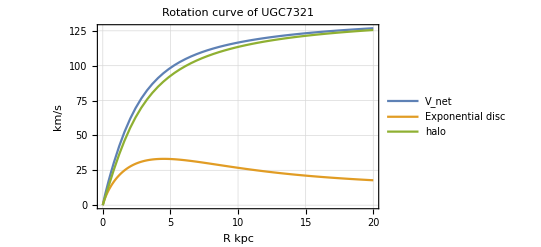

```mathematica
Plot[{Vnetugc[R*1000](3.086  10^13),Vdugc[R*1000](3.086  10^13),Vhalougc[R*1000](3.086  10^13)},{R,0,20},FrameLabel->{HoldForm[R kpc],HoldForm[km/s]},PlotLabel->HoldForm[Rotation curve of UGC7321],LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{"V_net","Exponential disc","halo"},{.8,.4}],GridLines->Automatic,Frame->True]
```

### Plots

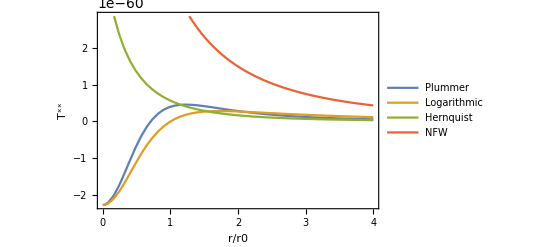

```mathematica
Plot[{Tplummer[r],Tlog[r],Thernquist[r],Tnfw[r]},{r,0,4},FrameLabel->{HoldForm[r/r0],HoldForm[T^xx]},PlotLegends->Placed[{"Plummer","Logarithmic","Hernquist","NFW"},{.5,.2}],LabelStyle->{GrayLevel[0]},Frame->True]
```

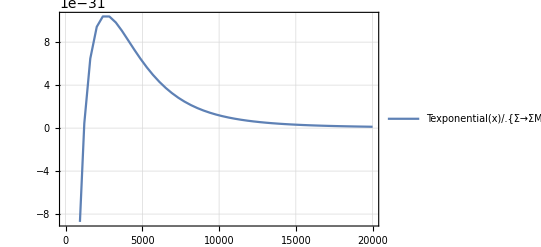

```mathematica
Plot[Texponential[x]/.{Σ -> ΣMilkyway,rd-> RdMilkyway},{x,0,20000},PlotRange->Automatic,PlotTheme->"Detailed"]
```

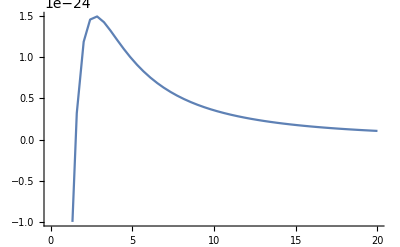

```mathematica
Plot[Thalo[x,0,0]/.{ρ-> ρMilkyway,rc-> RcMilkyway},{x,0,20}]
```

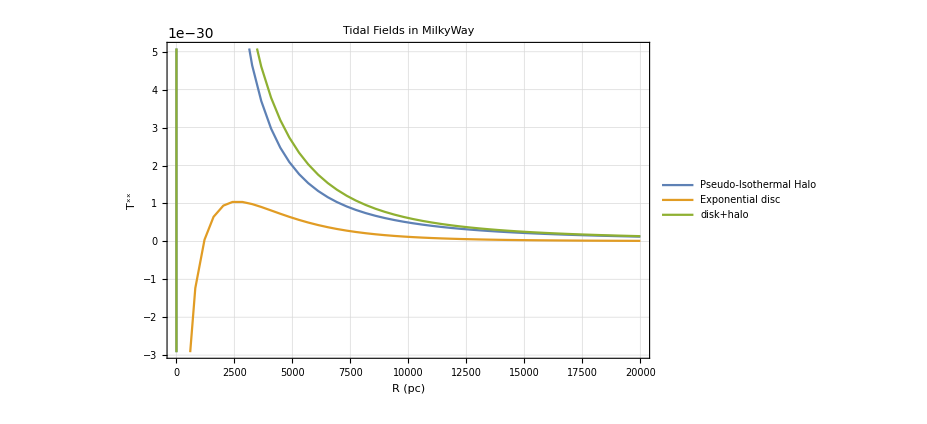

```mathematica
Plot[{Thalo[x,0,0]/.{ρ-> ρMilkyway,rc-> RcMilkyway},Texponential[x]/.{Σ -> ΣMilkyway,rd-> RdMilkyway},Thaloplusexp[x,0,0]/.{ρ-> ρMilkyway,rc-> RcMilkyway,Σ -> ΣMilkyway,rd-> RdMilkyway}},{x,0,20000},PlotLegends->Placed[{"Pseudo-Isothermal Halo","Exponential disc","disk+halo"},{.8,.7}],FrameLabel->{HoldForm[R "(pc)"],HoldForm[T^xx]},LabelStyle->{GrayLevel[0]},Frame->True,PlotTheme->"Detailed",PlotLabel->HoldForm["Tidal Fields in MilkyWay"],LabelStyle->Directive[Bold, Medium],PlotRange->Automatic]
```

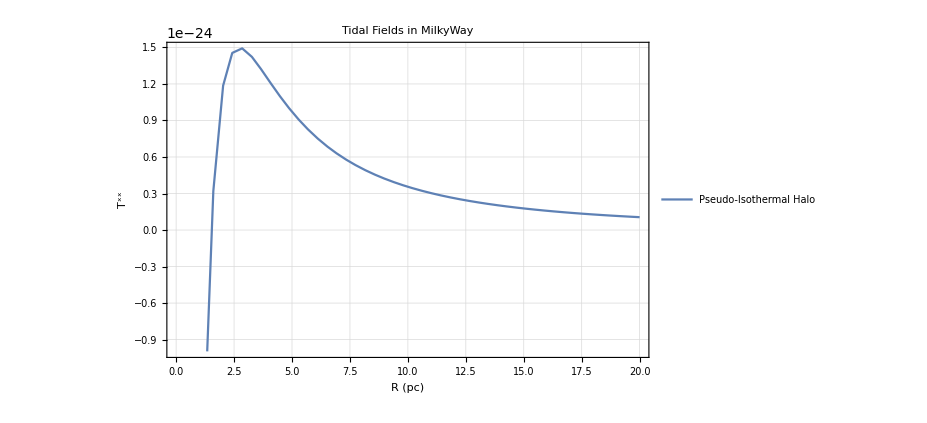

```mathematica
Plot[Thalo[x,0,0]/.{ρ-> ρMilkyway,rc-> RcMilkyway},{x,0,20},PlotLegends->Placed[{"Pseudo-Isothermal Halo"},{.8,.7}],FrameLabel->{HoldForm[R "(pc)"],HoldForm[T^xx]},LabelStyle->{GrayLevel[0]},Frame->True,PlotTheme->"Detailed",PlotLabel->HoldForm["Tidal Fields in MilkyWay"],LabelStyle->Directive[Bold, Medium],PlotRange->Automatic]
```

```mathematica
Plot[ {Thalo[x,0,0,ρMilkyway,RcMilkyway],Texponential[x,ΣMilkyway,RdMilkyway],Thalo[x,0,0,ρMilkyway,RcMilkyway]+Texponential[x,ΣMilkyway,RdMilkyway]} ,{x,0,10^30},PlotLegends->Placed[{"Pseudo-Isothermal Halo","Exponential disc","disk+halo"},{.8,.7}],PlotRange->Automatic]
```

-Graphics-

```mathematica
Plot[Thalo[x,0,0,ρMilkyway,RcMilkyway]+Texponential[x,ΣMilkyway,RdMilkyway],{x,0,8},FrameLabel->{HoldForm[r/r0],HoldForm[T^xx]},PlotLegends->Placed[{"Pseudo-Isothermal Halo+Exponential disc"},{.6,.3}],LabelStyle->{GrayLevel[0]},Frame->True,PlotRange->{-5,5}]
```

-Graphics-

```mathematica
Vd[R_] :=   √((2*Pi*G*Σ0/r0)(R^2 BesselI[0,R/r0] BesselK[0,R/r0]-R^2 BesselI[1,R/r0] BesselK[1,R/r0]))
```

```mathematica
Function[R,√(((4 π G Σ0) (R^2 BesselI[0,R/r0] BesselK[0,R/r0]-R^2 BesselI[1,R/r0] BesselK[1,R/r0]))/r0)]
```

Function[R,√(((4 π G Σ0) (R^2 BesselI[0,R/r0] BesselK[0,R/r0]-R^2 BesselI[1,R/r0] BesselK[1,R/r0]))/r0)]

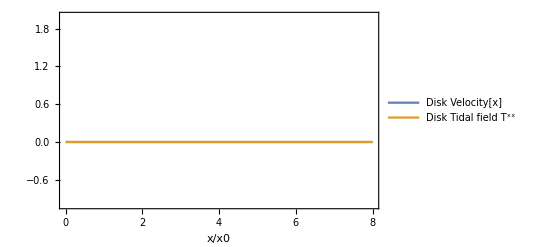

```mathematica
Plot[{Vd[r],Vd[r]^2/r,Texponential[r]},{r,0,8},FrameLabel->{HoldForm[x/x0]},PlotLegends->Placed[{"Disk Velocity[x]","Disk Tidal field T^xx"},{.6,.2}],LabelStyle->{GrayLevel[0]},Frame->True,PlotRange->{-1,2}]
```

```mathematica
Plot[{Vd[r,1,1],Texponential[r,1,1]},{r,0,10}]
```

-Graphics-